```mathematica
Clear[h,Δ,kx,ky,H,Δuu,Δud,Δdu,Δdd]
ξ[kx_,ky_]=(1-Cos[kx]-Cos[ky]);
h[kx_,ky_]=ξ[kx,ky]*PauliMatrix[0]+{bx,by,bz}.Table[PauliMatrix[i],{i,3}];

Δuu[kx_,ky_]=Sin[kx]-ⅈ Sin[ky];
Δdd[kx_,ky_]=Sin[kx]+ⅈ Sin[ky];
Δud[kx_,ky_]=-(sx*Cos[kx]+sy*Cos[ky]);
Δdu[kx_,ky_]=+(sx*Cos[kx]+sy*Cos[ky]);
Δ[kx_,ky_]={{Δuu[kx,ky],-Δud[kx,ky]},{Δdu[kx,ky],-Δdd[kx,ky]}};
(*Hpr[kx_,ky_]=ArrayFlatten[{{h[kx,ky],0*Δ[kx,ky]},{0*Δ[kx,ky]*,-h[kx,ky]*}}];*)
Hpr[kx_,ky_]=ArrayFlatten[{{h[kx,ky],0},{0,-PauliMatrix[3].h[kx,ky]*.PauliMatrix[3]}}];
H[kx_,ky_]=Refine[Hpr[kx,ky],{bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,kx∈Reals,ky∈Reals}];
```

```mathematica
H[kx,ky]
%//MatrixForm
```

{{1+bz-Cos[kx]-Cos[ky],bx-ⅈ by,0,0},{bx+ⅈ by,1-bz-Cos[kx]-Cos[ky],0,0},{0,0,-1-bz+Cos[kx]+Cos[ky],bx+ⅈ by},{0,0,bx-ⅈ by,-1+bz+Cos[kx]+Cos[ky]}}

(1+bz-Cos[kx]-Cos[ky] | bx-ⅈ by | 0 | 0
bx+ⅈ by | 1-bz-Cos[kx]-Cos[ky] | 0 | 0
0 | 0 | -1-bz+Cos[kx]+Cos[ky] | bx+ⅈ by
0 | 0 | bx-ⅈ by | -1+bz+Cos[kx]+Cos[ky])

```mathematica
UP = KroneckerProduct[PauliMatrix[1],PauliMatrix[3]];
Refine[H[kx,ky]+UP.H[-kx,-ky]*.UP,{bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,kx∈Reals,ky∈Reals}];
%//MatrixForm
UC = KroneckerProduct[PauliMatrix[1],PauliMatrix[2]];
Refine[H[kx,ky]+UC.H[kx,ky].UC,{bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,kx∈Reals,ky∈Reals}];
%//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(2 bz | 0 | 0 | 0
0 | -2 bz | 0 | 0
0 | 0 | -2 bz | 0
0 | 0 | 0 | 2 bz)

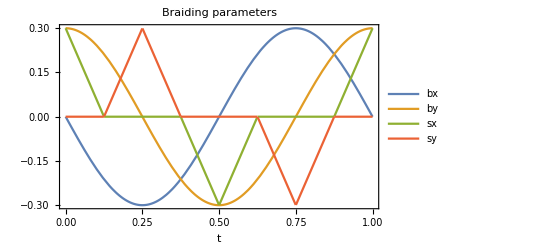

```mathematica
b0=-.3;
s0=+.3;
Bx[t_]:= +b0*Sin[t*2π]
By[t_]:= -b0*Cos[t*2π]
Sx[t_]:=s0*Piecewise[{ {1-1/.125t,0≤t≤.125},{-1/.125(t-.375),.375<t≤.5},{-1+1/.125(t-.5),.5<t≤.625},{+1/.125(t-.875),.875<t≤1}}]
Sy[t_]:=s0*Piecewise[{ {1/.125(t-.125),.125<t≤.25}, {1-1/.125(t-.25),.25<t≤.375}, {-1/.125(t-.625),.625<t≤.75}, {-1+1/.125(t-.75),.75<t≤.875}}]
Plot[{Bx[t],By[t],Sx[t],Sy[t]},{t,0,1},Frame->True,FrameLabel->{"t"},PlotLegends->{"bx","by","sx","sy"},PlotLabel->"Braiding parameters"]
```

```mathematica
Refine[H[kx,ky]-H[kx,ky]†,{bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,kx∈Reals,ky∈Reals}]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Clear[kx,ky,eval]
eval[kx_,ky_]=Eigenvalues[H[kx,ky]];

(* set the system dimensions *)
Lx=Ly=7;
```

```mathematica
spectrum={};
Monitor[
Do[
tp ={};
Do[
AppendTo[tp,Flatten[eval[kx,ky]/.{bx->Bx[t],by->By[t],bz->0.,t0->1.,sx->Sx[t],sy->Sy[t]}]];
,{kx,0,2π-2π/Lx,2π/Lx},{ky,0,2π-2π/Lx,2π/Ly}];
tp =Sort[Flatten[tp]];
If[Length[tp]>40,
AppendTo[spectrum,tp[[Length[tp]/2-20;;Length[tp]/2+21]]];
,
AppendTo[spectrum,tp];
];
,{t,0.,1,.01}]
,t]
```

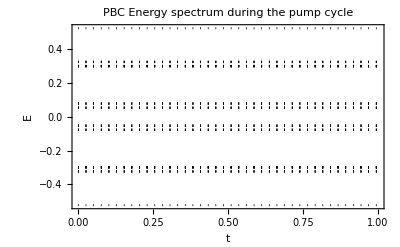

```mathematica
bulk =ListPlot[spectrumᵀ,PlotRange->Full,PlotStyle->Directive[{Black,Dotted}],Joined->True,DataRange->{0,1},Frame->True,FrameLabel->{"t", "E"},PlotLabel->"PBC Energy spectrum during the pump cycle"]
```

```mathematica
(* almost-by-hand FT *)
Clear[δ,Hrs]
(H[kx,ky]*Exp[ⅈ*{kx,ky}.({x1,y1}-{x2,y2})]//TrigToExp//ExpandAll)/.{ⅇ^(ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)->δ[x1,x2]*δ[y1,y2],ⅇ^(-ⅈ kx+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)->δ[x1,x2+1]*δ[y1,y2],ⅇ^(ⅈ kx+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)-> δ[x1+1,x2]*δ[y1,y2],ⅇ^(-ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)-> δ[x1,x2]*δ[y1,y2+1],ⅇ^(ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)-> δ[x1,x2]*δ[y1+1,y2]};
(* assign local real space Hamiltonian *)
Hrs[x1_,x2_,y1_,y2_]=%;
δ[x_,y_]=If[x==y,1,0];

(* now construct the full one *)
Clear[Hfull]
pbc=True;
Hfull= ConstantArray[0,{Lx,Ly,4,Lx,Ly,4}];
Do[
If[x1>0&&x1≤Lx&&y2>0&&y2≤Ly,
Hfull[[x1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];

(* the boundary terms *)
If[x1==Lx+1&&y2>0&&y2≤Ly&&pbc,
Hfull[[1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];
If[y2==Ly+1&&x1>0&&x1≤Lx&&pbc,
Hfull[[x1,y1,;;,x2,1,;;]]+=Hrs[x1,x2,y1,y2];
];

If[x1==0&&y2>0&&y2≤Ly&&pbc,
Hfull[[Lx,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];
If[y2==0&&x1>0&&x1≤Lx&&pbc,
Hfull[[x1,y1,;;,x2,Ly,;;]]+=Hrs[x1,x2,y1,y2];
];
,{x1,x2-2,x2+2},{x2,Lx},{y1,Ly},{y2,y1-1,y1+1}]
Hfull=ArrayReshape[Hfull,{Lx*Ly*4,Lx*Ly*4}];

(* diagonalize and plot *)
Clear[t]
specPBC={};
states={};
Monitor[
Do[
{evals,evec}=Eigensystem[N[Hfull/.{bx->Bx[t],by->By[t],bz->0.,t0->-1.,sx->Sx[t],sy->Sy[t]}]];
order=Ordering[evals];
evals = evals[[order]];
evec=evec[[order]];
If[Length[evals]>40,
AppendTo[specPBC,evals[[Length[evals]/2-20;;Length[evals]/2+21]]];
,
AppendTo[specPBC,evals];
];
(*AppendTo[states,evec];*)
,{t,0.,1,.01}]
,t]
```

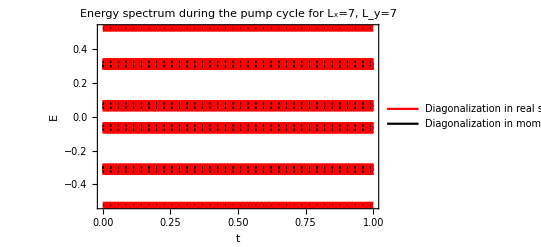

```mathematica
Show[ListPlot[Chop[specPBCᵀ],PlotStyle->Directive[Thickness[.0125],Red],PlotLegends->LineLegend[{Red,Black},{"Diagonalization in real space with PBC", "Diagonalization in momentum space"}],Joined->True,PlotRange->Full,DataRange->{0,1}],bulk,Frame->True,Axes->False,FrameLabel->{"t","E"},PlotLabel->"Energy spectrum during the pump cycle for L_x="<>ToString[Lx]<>", L_y="<>ToString[Ly]]
```

```mathematica
(* now construct the full one *)
Clear[Hfull]
pbc=False; (* this time for OBC!! *)
Hfull= ConstantArray[0,{Lx,Ly,4,Lx,Ly,4}];
Do[
If[x1>0&&x1≤Lx&&y2>0&&y2≤Ly,
Hfull[[x1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];

(* the boundary terms *)
If[x1==Lx+1&&y2>0&&y2≤Ly&&pbc,
Hfull[[1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];
If[y2==Ly+1&&x1>0&&x1≤Lx&&pbc,
Hfull[[x1,y1,;;,x2,1,;;]]+=Hrs[x1,x2,y1,y2];
];

If[x1==0&&y2>0&&y2≤Ly&&pbc,
Hfull[[Lx,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];
If[y2==0&&x1>0&&x1≤Lx&&pbc,
Hfull[[x1,y1,;;,x2,Ly,;;]]+=Hrs[x1,x2,y1,y2];
];
,{x1,x2-1,x2+1},{x2,Lx},{y1,Ly},{y2,y1-1,y1+1}]
Hfull=ArrayReshape[Hfull,{Lx*Ly*4,Lx*Ly*4}];

(* diagonalize and plot *)
Clear[t]
specOBC={};
states={};
Monitor[
Do[
{evals,evec}=Eigensystem[N[Hfull/.{bx->Bx[t],by->By[t],bz->0.,t0->-1.,sx->Sx[t],sy->Sy[t]}]];
order=Ordering[evals];
evals = evals[[order]];
evec=evec[[order]];
If[Length[evals]>40,
AppendTo[specOBC,evals[[Length[evals]/2-20;;Length[evals]/2+21]]];
,
AppendTo[specOBC,evals];
];
(*AppendTo[states,evec];*)
,{t,0.,1,.025}]
,t]
```

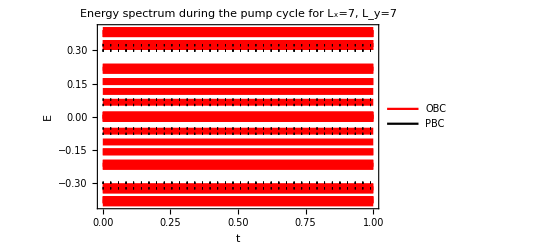

```mathematica
Show[ListPlot[Chop[specOBCᵀ],PlotStyle->Directive[Thickness[.0125],Red],PlotLegends->LineLegend[{Red,Black},{"OBC", "PBC"}],Joined->True,DataRange->{0,1}],bulk,Frame->True,Axes->False,FrameLabel->{"t","E"},PlotLabel->"Energy spectrum during the pump cycle for L_x="<>ToString[Lx]<>", L_y="<>ToString[Ly],PlotRange->{-1,1}.4]
```